```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[If[ii≥1,n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],BW[w,wr,Γ,δbg,const,shift,shift2],{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->20000,Method->"LevenbergMarquardt"],{i,Length[hwhmi]}]];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,1,Length[res]}];Export["spectraldata/Npartscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])(const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,1,Length[res]}];Export["spectraldata/Npartscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Npartscan/results/"<>ToString[res]<>".dat"];
```

## Npart scan

```mathematica
NpartbTab={{2,14.389652416369772},{12,12.717953496804803},{22,11.96362371585272},{32,11.407195471353292},{42,10.944130215625353},{52,10.536848008019458},{62,10.167117535602095},{72,9.82456720817997},{82,9.50267991365668},{92,9.197048928943842},{102,8.904495082078075},{112,8.622665576572569},{122,8.349731370939708},{132,8.084234479882952},{142,7.824988928460424},{152,7.570988742407739},{162,7.321387318428727},{172,7.075424898585875},{182,6.832441631267922},{192,6.591812582479472},{202,6.35297312520492},{212,6.115363748462073},{222,5.878450214476514},{232,5.6416848545100216},{242,5.404503991825351},{252,5.166316935797287},{262,4.926459291715929},{272,4.684220954100872},{282,4.4387313721772035},{292,4.189025280552304},{302,3.9338337411989226},{312,3.671647257166055},{322,3.4003848421919827},{332,3.1172793371708747},{342,2.8182718843271655},{352,2.497107666359125},{362,2.143197748173256},{372,1.7356098497264896},{382,1.2200001148282844},{392,0.12304283392723618}};
```

```mathematica
NpartT={{382.7,164.1,3.4},{329.4,164.1,3.5},{260.1,164.7,4.6},{185.5,165.8,4.4},{128.5,167.3,4.9},{84.705,166.8,4.9},{52.41,164.1,3.7},{29.77,159.0,4.0}};
```

```mathematica
Do[ccdata[n]=Import["spectraldata/Npartscan/cc/swccNpart"<>ToString[Round[NpartT[[n,1]]]]<>"spectra.dat"];,{n,Length[NpartT]}];
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Npartscan/cc/swccNpart"<>ToString[Round[NpartbTab[[n,1]]]]<>"uspectra.dat"];,{n,Length[NpartbTab]}]; 
Do[ccdatal[n]=Import["spectraldata/Npartscan/cc/swccNpart"<>ToString[Round[NpartbTab[[n,1]]]]<>"lspectra.dat"];,{n,Length[NpartbTab]}];
```

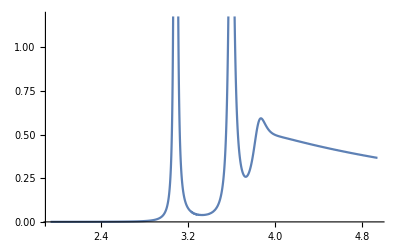

```mathematica
ListPlot[ccdatal[2],Joined->True]
```

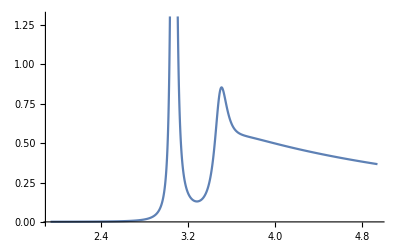

```mathematica
ListPlot[ccdata[8],Joined->True]
```

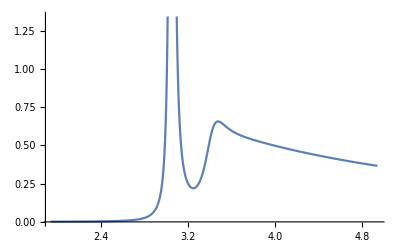

```mathematica
ListPlot[ccdatau[2],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodel,ccmodell,ccmodelu]
fitnew[ccdata,ccmodel,Length[NpartT]];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
fitnew[ccdatau,ccmodelu,Length[NpartbTab]];
fitnew[ccdatal,ccmodell,Length[NpartbTab]];
```

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Do[If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];,{i,Length[ccmodelu]}];
Do[If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodell]}];
```

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc,wrfitccu,gfitccu,areafitccu,cfitccu,dfitccu,sfitccu,s2fitccu,wrfitccl,gfitccl,areafitccl,cfitccl,dfitccl,sfitccl,s2fitccl];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
```

```mathematica
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitccu,ccmodelu];
store[const,cfitccu,ccmodelu];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitccu,ccmodelu];
store[wr,wrfitccl,ccmodell];
store[Γ,gfitccl,ccmodell];
store[const,cfitccl,ccmodell];
store[δbg,dfitccl,ccmodell];
store[shift,sfitccl,ccmodell];
store[shift2,s2fitccl,ccmodell];
storearea[areafitccl,ccmodell];
```

### Import previous results

```mathematica
import[wrfitcc];
import[gfitcc];
import[cfitcc];
import[dfitcc];
import[sfitcc];
import[s2fitcc];
import[areafitcc];
import[wrfitccu];
import[gfitccu];
import[cfitccu];
import[dfitccu];
import[sfitccu];
import[s2fitccu];
import[areafitccu];
import[wrfitccl];
import[gfitccl];
import[cfitccl];
import[dfitccl];
import[sfitccl];
import[s2fitccl];
import[areafitccl];
```

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,2,1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

### Dilepton ratio

```mathematica
Tmu={0.15485899763908725,0.0016486158206386965};
Tmu17={0.13503791802191306,0.22227908563630164};
```

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
nBi[w_,T_]:=NIntegrate[p^2 nB[√(w^2+p^2),T] w/(√(w^2+p^2)),{p,0,∞}];
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={NpartT[[ii,1]],Emfactor (areafitcc[[ii,2]]nBi[wrfitcc[[ii,2]],NpartT[[ii,2]]/1000])/(areafitcc[[ii,1]]nBi[wrfitcc[[ii,1]],NpartT[[ii,2]]/1000])}],{ii,Length[R0]}];
```

```mathematica
R0u=ConstantArray[0,Length[wrfitccu]];
Do[If[Length[wrfitccu[[ii]]]==2,R0u[[ii]]={NpartbTab[[ii,1]],Emfactor (areafitccu[[ii,2]]nB[wrfitccu[[ii,2]],Tmu[[1]]])/(areafitccu[[ii,1]]nB[wrfitccu[[ii,1]],Tmu[[1]]])}],{ii,Length[R0u]}];
R0l=ConstantArray[0,Length[wrfitccl]];
Do[If[Length[wrfitccl[[ii]]]==2,R0l[[ii]]={NpartbTab[[ii,1]],Emfactor (areafitccl[[ii,2]]nB[wrfitccl[[ii,2]],Tmu[[1]]])/(areafitccl[[ii,1]]nB[wrfitccl[[ii,1]],Tmu[[1]]])}],{ii,Length[R0l]}];
```

```mathematica
R0=DeleteCases[R0,0];
```

```mathematica
R0u=DeleteCases[R0u,0];
R0l=DeleteCases[R0l,0];
```

```mathematica
R0
```

{{382.7,0.0467362},{329.4,0.0467362},{260.1,0.0468858},{185.5,0.0469838},{128.5,0.0466126},{84.705,0.0468208},{52.41,0.0467362},{29.77,0.0433711}}

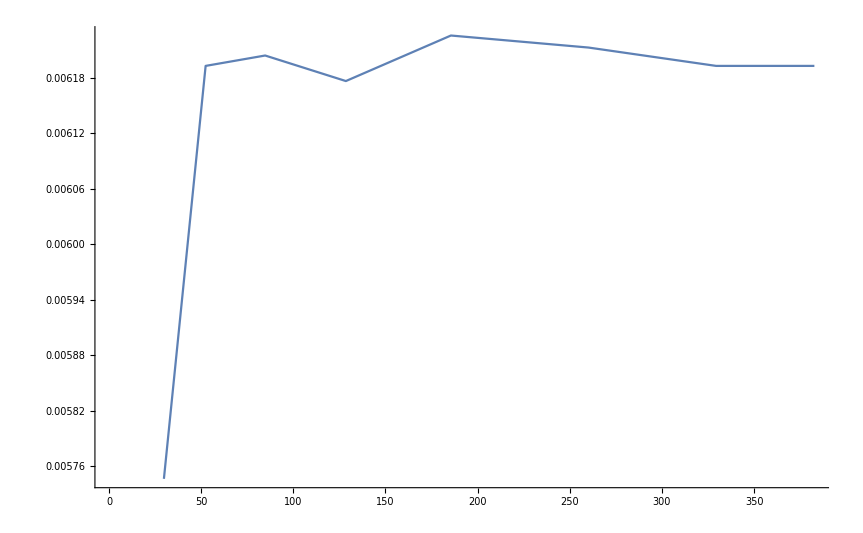

```mathematica
ListPlot[R0/.{a_,b_}:>{a,b 0.1325},Joined->True]
```

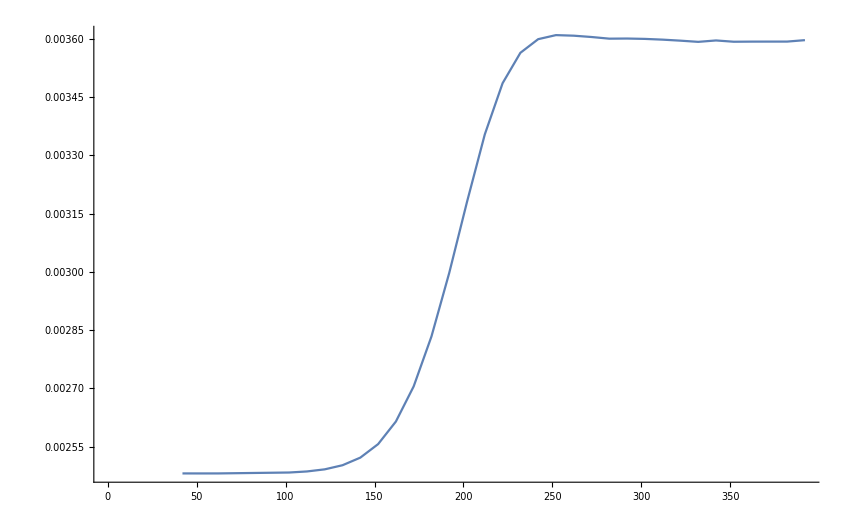

```mathematica
ListPlot[Join[(R0/.{a_,b_}:>{a,b 0.1325})[[;;3]],(R0/.{a_,b_}:>{a,b 0.1325})[[7;;]]],Joined->True]
```